## Simple Hexapod Model

Defines the equations of motion for a tripod gait Hexapod using principal connections, then simulates a walking gait.  Currently, the graphics look bogus because the principal connection uses an approximation that only works for (very) small angles.  Working out what it takes to get the gait to work for larger angles.

Author: 	Patricio Vela

Created: 	June 30, 2003
Modified: 	March 08,2015

Notes:
  - Redone to work.
  - Requires some updating still since Mathematica has changed.

## Initialization

### Load Libraries

```mathematica
(* Load Geometric Mechanics and Dynamical Systems libraries for this example. *)
AppendTo[$Path,ToFileName[{$HomeDirectory,"Mathematica"}]];
<<ivamatica/defpackages.m
LoadPackages[TANGENTS+TPRINCIPAL]
DoneLoading

(* Additional basic math functions. *)
<<ivamatica/Basic/extras.m

(* For dealing with equations of motion. *)
<<ivamatica/Dynamics/equations.m
<<ivamatica/Dynamics/averaging.m

(* Lagrangian mechanics.    Are they really needed? *)
<<ivamatica/Mechanics/constraints.m
<<ivamatica/Mechanics/kinematics.m
<<ivamatica/Mechanics/lagrangian.m

(* For creating visual movie output. *)
<<ivamatica/Graphics/anim.m
```

UpSetDelayed::write: Tag Integer in oInit[Binary, len_Integer] is Protected.

UpSetDelayed::write: Tag Integer in oInit[Binary, len_Integer, val_Integer] is Protected.

UpSetDelayed::write: Tag Integer in oSet[Binary[b_], val_Integer] is Protected.

General::stop: Further output of UpSetDelayed :: write will be suppressed during this calculation.

Loaded Euclidean package 
Loaded Fiber Bundles package 
Loaded Manifolds package 
Loaded Vectors package 
Loaded Tangents package 
Loaded Tangent Fiber Bundles package 
Loaded Tangent Manifolds package 
Loaded Lie Groups package 
Loaded Tangent Lie Groups package 
Loaded Principal Bundles package 
Loaded Tangent Principal Bundles package

Removed package loading variables.

```mathematica
(* Define the principal bundle structure. *)
M = Euclidean;
TM = TEuclidean;

G=SE2;
𝔤 = se2;
SuperStar[𝔤] = dse2;
TG = TSE2;
tG = SE2xse2;
dG = SE2xdse2;

Q=PrincipalBundle`ExSE2;
TQ = TPrincipalBundle`TExTSE2;
CO = Configuration;

(* This is all overkill.  It was defined in order to work out the constrained Lagrangian associated to a tripod stance. I am actually doing it differently by working out the parallel mechanics. Once I get a feel for the feasibility of the answer, I may go back and try to derive it this way. - PAV 2015/03/08. *)
```

```mathematica
Off[General::spell1];
Off[General::spell];
```

### Configuration space and other variables

```mathematica
(* Define basic elements. *)
g = oInit[G, x, y, θ];
dimG=gDim[g];

g' = oInit[Vector, Table[ gLocal[g][[i]]' , {i, dimG}] ];
gdot = oInit[Vector, Table[OverDot[gLocal[g][[i]]],{i,dimG}]];

gp = oInit[TG , g, g']

r = oInit[M, {ϕ1, ϕ2, Right, Left}]; (* This definition is abusive.  Need to fix later.*)
r' = oInit[Vector, Table[ gLocal[r][[i]]' , {i, gDim[r]}]];
rdot = oInit[Vector, Table[OverDot[gLocal[r][[i]]],{i,gDim[r]}]];
dimM = gDim[r];

ξ = oInit[𝔤, { ξ1 , ξ2, ξ3}];
e = oInit[𝔤, { e1, e2, e3}];
q =  oInit[Q, r, g]
qp = oInit[TQ, r, g, r', g']
```

(x'
y'
θ')_(x
y
θ)

Group  Fiber {x, y, θ} with base {ϕ1, ϕ2, Right, Left}

Tangent Vector {{ϕ1', ϕ2', Right', Left'}, {x', y', θ'}} of principal fiber bundle at the point {{ϕ1, ϕ2, Right, Left}, {x, y, θ}}

### Constants of the discrete crawler

```mathematica
doSim=1;
If[doSim==1,
legLen = 1;
bodyLen = 3/2;
,
Clear[ legLen, bodyLen];
];
```

### Define Hexapod Graphic.

```mathematica
XWIN = {5.1,10.1};
YWIN = {10.1, 10.1};
GRDX= {-25,70};
GRDY = { -25, 40};
GSTP = 3;
CSTP = 1.5;
pegrad = legLen/10;
XLen = bodyLen/2;
HexapodParams = {AspectRatio->Automatic,Axes->{False,False}, Frame->True, FrameTicks->{{},{}}};


gHex2D[Q[q_], params___] := Module[{x, y, θ,gc,rc, gf, gb, g1, g2, g3, g4, g5, g6, gfx, angles, r1, r2, r3, xcent, ycent},
gc = gGroup[Q[q]];
{x, y} = gPosition[gc];
rc = gBase[Q[q]];
gf = gc·oInit[G, {1/2 bodyLen, 0, 0}];
gb = gc ·oInit[G, {-1/2 bodyLen, 0, 0}];
gfx = {Line[{gPosition[gf], gPosition[gb]}]};

g1 = gf ·( oInit[G, {0,0,-2 gLocal[rc][[1]]}]·oInit[G, {0,legLen,0}]);
gfx = Append[gfx,Line[{gPosition[gf], gPosition[g1]}]];
g2 = gc ·(oInit[G, {0,0,-gLocal[rc][[2]]}] · oInit[G, {0,legLen,0}]);
gfx = Append[gfx,Line[{gPosition[gc], gPosition[g2]}]];
g3 = gb ·( oInit[G, {0,0,-2 gLocal[rc][[1]]}]·oInit[G, {0,legLen,0}]);
gfx = Append[gfx,Line[{gPosition[gb], gPosition[g3]}]];
g4 = gb ·( oInit[G, {0,0,2 gLocal[rc][[2]]}]·oInit[G, {0,-legLen,0}]);
gfx = Append[gfx,Line[{gPosition[gb], gPosition[g4]}]];
g5 = gc ·( oInit[G, {0,0,gLocal[rc][[1]]}]·oInit[G, {0,-legLen,0}]);
gfx = Append[gfx, Line[{gPosition[gc], gPosition[g5]}]];
g6 = gf ·( oInit[G, {0,0,2 gLocal[rc][[2]]}]·oInit[G, {0,-legLen,0}]);
gfx = Append[gfx,Line[{gPosition[gf], gPosition[g6]}]];

gfx = Append[gfx, If[  gLocal[rc][[3]] == 1, 
{Disk[ gPosition[g1],pegrad],Circle[ gPosition[g2],pegrad],
Disk[ gPosition[g3],pegrad],Circle[ gPosition[g4],pegrad],
Disk[ gPosition[g5],pegrad],Circle[ gPosition[g6],pegrad]}
,{Circle[ gPosition[g1],pegrad],Disk[ gPosition[g2],pegrad],
Circle[ gPosition[g3],pegrad],Disk[ gPosition[g4],pegrad],
Circle[ gPosition[g5],pegrad],Disk[ gPosition[g6],pegrad]}
 ]];
gfx = Append[gfx, { RGBColor[0,1,0], Circle[{0,0},legLen/5]}];
gfx = Append[gfx,fMakeGrid[GRDX, GRDY, GSTP]];
Graphics[gfx,Join[{ PlotRange->{{x -XWIN[[1]],x+XWIN[[2]]},{y-YWIN[[1]],y+YWIN[[2]]}}}, params]]
]

gHex2D[Q[q_], G[gdes_], params___] := Module[{x, y, θ, gfx, angles, r1, r2, r3},
gc = gGroup[Q[q]];
{x, y} = gPosition[gc];
rc = gBase[Q[q]];

gfx = {gHex2D[Q[q]][[1]]};
plot1 = {gPosition[G[gdes]·oInit[G, {-1/8 XLen , 0, 0}]], gPosition[ G[gdes] ·oInit[G, {1/4 XLen , 0, 0}]]};gfx = Append[gfx, {RGBColor[0,0,1], Line[plot1]}];
gfx=Append[gfx,{RGBColor[0,0,1],Disk[gPosition[G[gdes]],1/40 XLen]}];
plot1 = {gPosition[G[gdes]· oInit[G,{0,1/8 XLen,0}]], gPosition[ G[gdes] ·oInit[G, {0 ,- 1/8 XLen, 0}]]};
gfx = Append[gfx, {RGBColor[0,0,1], Line[plot1]}];
{x, y} = gPosition[G[gdes]];

Graphics[gfx,Join[{ PlotRange->{{x -XWIN[[1]],x+XWIN[[2]]},{y-YWIN[[1]],y+YWIN[[2]]}}}, params]]
]
```

## Equations of Motion

### Local Form of the Principal Connection

```mathematica
r𝒜 = oInit[𝔤, {legLen, 0, -1}];
l𝒜 = oInit[𝔤, {legLen, 0, 1}];
```

## Simulations

### Open Loop Control

#### Gait Parametrization

```mathematica
ψ̄ = 0; ψ̃ = 30 π/180;
ω = 5;
ϵ = 1;
Τ=2 π ϵ/ω;
```

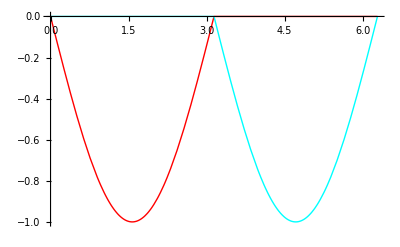

```mathematica
f[t_] := {-Sin[t], Sin[t]};
v1[t_] :=  Which[ Mod[t, 2π]≤ π , 1, Mod[t, 2π]≤  2π, 0, True, 0]   f[t][[1]];
v2[t_] := Which[ Mod[t, 2π]≤ π , 0, Mod[t, 2π] ≤ 2π, 1, True, 0]    f[t][[2]];
Plot[{v1[t], v2[t]}, {t, 0, 2 π}, PlotStyle-> {RGBColor[1,0,0], RGBColor[0,1,1]}] 
xover = Τ/2;
```

#### Simulation proper

```mathematica
t0 = 0;
t1 = 20 Τ
```

8 π

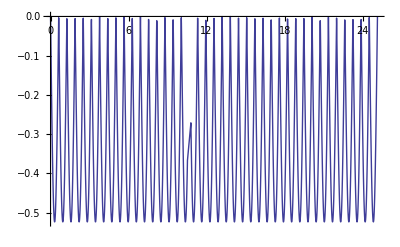
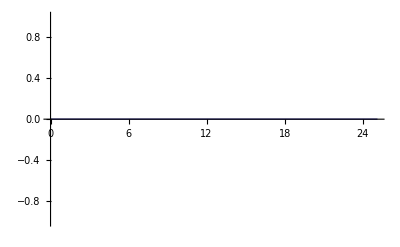
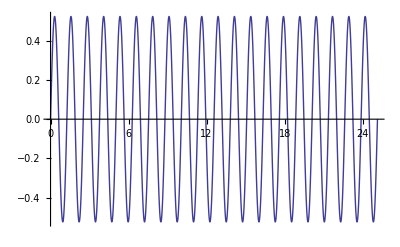

```mathematica
𝒜[tt_] := v1[tt] r𝒜 + v2[tt] l𝒜;
Table[ Plot[gLocal[𝒜[(ω t)/ϵ]][[i]],{t,0,t1}],{i,dimG}]
```

```mathematica
gsol = NDSolve[ -𝒜[ (ω t)/ϵ] , oInit[G,{0,0,0}],g,{t,t0, t1}, MaxSteps -> 10000]
rft[tt_] := Module[{t},oInit[M,Flatten[{∫f[ (ω t)/ϵ] ⅆt /. {t -> Mod[tt,Τ]}, If[v1[(ω tt)/ϵ] ≠ 0, {1,0},{0,1}]}]]];
gft[t_] := oInit[G,Flatten[Table[ gLocal[g][[i]][t] /. gsol , {i, 1, gDim[g]}]]];
qft[t_] := oInit[Q, rft[t], gft[t]];
gdes[t_] := oInit[G,{0,0,0}];
```

{{x→InterpolatingFunction[{{0.,25.1327}},<>],y→InterpolatingFunction[{{0.,25.1327}},<>],θ→InterpolatingFunction[{{0.,25.1327}},<>]}}

### Lie Group Control

```mathematica
(* Specify the desired path/trajectory type, the gains, and the error function. *)
despath = 1;
Which[despath == 1, k = {4, 4,1/2}, despath == 2, k = {4, 4,1/2}];
errF[G[gerr_]] := Module[ {f1, f2, α1, α2} , 
f1 =-k[[1]] gerr[[1]];
f2 = ( k[[2]] ArcTanH[ gerr[[1]], gerr[[2]] ] + k[[3]] gerr[[3]]);
{α1, α2} = 1/π{{1, 1},{-1, 1}}.{f1, f2}
];

Clear[α, xover, gsol];
Remove[gdes];
```

```mathematica
(* Setup the oscillatory control parameters. *)
ω=1;
ϵ=1/6;
Τ = (2 π ϵ)/ω;
xover = π;

f[t_] := { α[[1]]Sin[t], α[[2]] Sin[t]};
v1[t_] := If[Mod[t,2 π] ≤ xover, 1,0] f[t][[1]];
v2[t_] := If[Mod[t, 2 π] ≤ xover,0,1]f[t][[2]];

𝒜[tt_] := v1[tt] r𝒜 + v2[tt] l𝒜;
```

```mathematica
(* Initial condition and trajectory to follow. *)
g0=oInit[G,{-1,-0.5,- π/8}];
(*g0=oInit[G,{xfun[0],yfun[0],ArcTan[Derivative[1][xfun][0], Derivative[1][yfun][0]]}];*)

Which[  
despath == 1,gdes[t_] := oInit[G, {1/2 t,0,0}],
despath == 2, gdes[t_] := oInit[G, {1/(2 √2) t, 1/(2 √2) t, ArcTan[1/(2 √2), 1/(2 √2)]}],
despath == 3, gdes[t_] := oInit[G, {xfun[t], yfun[t], ArcTan[Derivative[1][xfun][t], Derivative[1][yfun][t]]}]];
```

```mathematica
tfac = 4; (* I have no idea what role these play, butneed to define in order to simulate. *)
nper = 17;

gcurr=g0;
gflow=Append[{},gcurr];
αmax = 1.5;

αflow = {};
xflow = {};
rflow = {};

maxsteps=40*0 + Floor[tfac*nper/Τ] ;
t0 = 0; t1 = maxsteps * Τ;

For[cnt=1,cnt<=maxsteps,cnt++,
α = errF[Inverse[gcurr] ·gdes[cnt*Τ]];
Which[α[[1]] > αmax, α[[1]] = αmax, α[[1]] < -αmax, α[[1]] = -αmax];
Which[α[[2]] >αmax, α[[2]] =αmax, α[[2]] < -αmax, err = αmax];

gsol[cnt] =  NDSolve[ -𝒜[(ω t)/ϵ] , gcurr,g,{t,0, Τ}];
gcurr=oInit[G,Flatten[Table[gLocal[g][[i]][Τ]/.gsol[cnt],{i,1,gDim[g]}]]];
gflow=Append[gflow,gcurr];
αflow = Append[αflow, α];

rflow = Append[rflow, ∫f[(ω t)/ϵ] ⅆt];
];
```

```mathematica
gft[t_]:=Module[{nt,tt},nt=Floor[t/Τ]+1;
If[nt≤maxsteps,tt=t-Floor[t/Τ] Τ,nt=maxsteps;
tt=Τ;];
oInit[G,Table[(gLocal[g][[i]][tt]/.gsol[nt])[[1]],{i,1,dimG}]]
];

Clear[dist, err];
rft[time_] := Module[{nt, tt}, nt = Floor[time/Τ] + 1;
If[nt≤maxsteps,tt=time-Floor[time/Τ] Τ,nt=maxsteps;
tt=Τ;];
oInit[M,Which[ tt ≤ ϵ/ω xover , Flatten[{rflow[[nt]] /. {t -> tt}, 1, 0}] , True, Flatten[{rflow[[nt]] /. {t -> tt},0, 1}]]]
];

qft[t_] := oInit[Q,rft[t], gft[t]];
```

## Visualizing Motion of the Hexapod

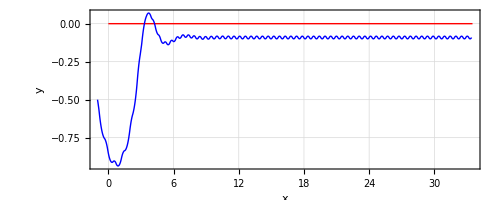

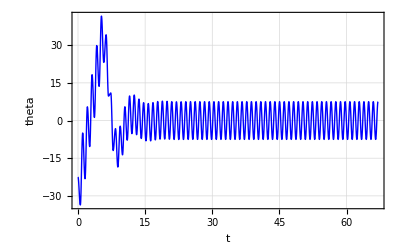

```mathematica
ParametricPlot[{gPosition[gdes[t]],gPosition[gft[t]]},{t,t0, t1},FrameLabel->{"x","y"},PlotRange->All, GridLines->Automatic, PlotStyle->{RGBColor[1,0,0], RGBColor[0,0,1]}, PlotRange -> All, Frame -> True]
Plot[gLocal[gft[t]][[3]]*180/π, {t,t0, t1},Frame->True,FrameLabel->{"t", "theta"},RotateLabel->False, PlotRange->All, GridLines->Automatic, PlotStyle -> {RGBColor[0,0,1]}, Compiled -> False]
```

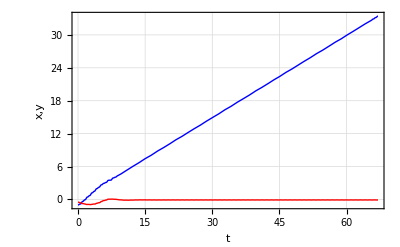

```mathematica
Plot[{gLocal[gft[t]][[1]], gLocal[gft[t]][[2]]}, {t, t0, t1},RotateLabel->False,FrameLabel->{"t", "x,y"},PlotRange->All, GridLines->Automatic, PlotStyle->{RGBColor[0,0,1], RGBColor[1,0,0]}, Frame -> True]
```

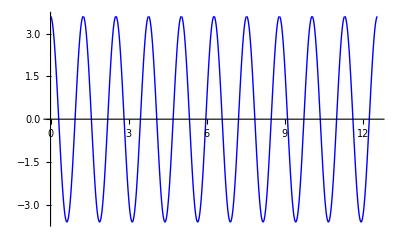

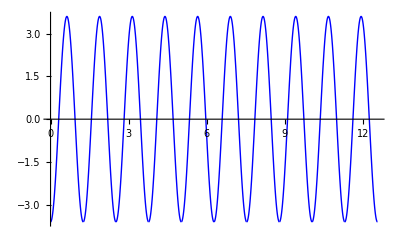

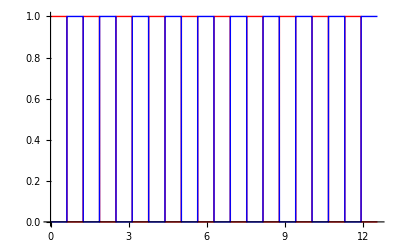

```mathematica
Plot[ 180/π gLocal[rft[t]][[1]], {t, t0, t1}, PlotStyle -> RGBColor[0,0,1]]
Plot[ 180/π gLocal[rft[t]][[2]], {t, t0, t1}, PlotStyle -> RGBColor[0,0,1]]
Plot[{gLocal[rft[t]][[3]], gLocal[rft[t]][[4]]},{t, t0, t1} ,PlotStyle ->{ RGBColor[1,0,0],RGBColor[0,0,1]}, PlotRange -> All]
```

## Animating the Hexapod

### Snapshots.

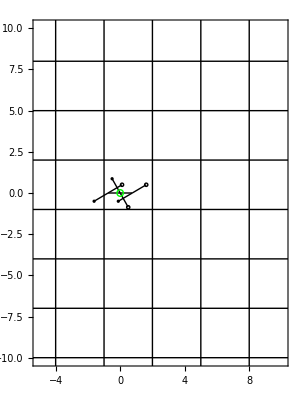

```mathematica
r0 = oInit[M, {π/6, -π/6, 0,1}];
g0 = oInit[G, {0,0,0}];
q0 = oInit[Q, r0, g0];
gHex2D[q0, HexapodParams] // Show
```

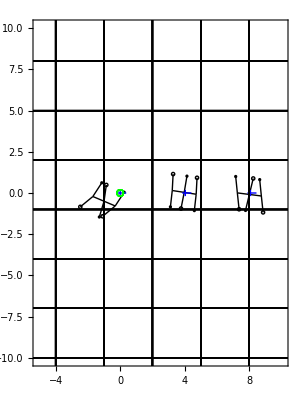

```mathematica
snaps = Table[gHex2D[qft[t],gdes[t],HexapodParams] , {t,t0, t1, (t1-t0)/8.3}];
last = gHex2D[qft[t1],gdes[t1],HexapodParams];
stills =  Table[ snaps[[i]][[1]], {i, 1, Length[snaps]}];
Graphics[{{RGBColor[0,0,1]}, stills}, snaps[[1]][[2]]] // Show
```

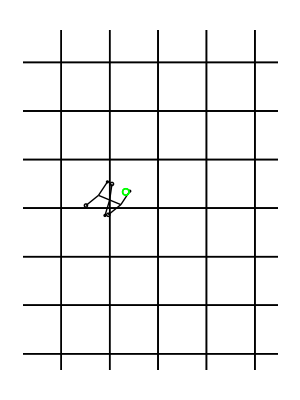

```mathematica
{gHex2D[qft[0]], gHex2D[qft[t1/2]], gHex2D[qft[t1]]} // Show
```

### Animation

```mathematica
Animate[ gHex2D[qft[t], gdes[t], HexapodParams], {t,t0,t1, Τ/10}]
```

```mathematica
(*--Exporting the Animation--*)
themovie = Table[ gHex2D[qft[t], gdes[t], Append[HexapodParams, DisplayFunction -> Identity]], {t,t0,t1, Τ/10}];
Length[themovie]
```

401

```mathematica
fMakeMovie["/tmp/pvela/movie","hexapod_tt02",themovie]
```

## Saving to file

```mathematica
stf = t1;
tg = Table[ Join[ {t} , gLocal[rft[t]] , gLocal[gft[t]], N[gLocal[gdes[t]]] ] , {t, 0, stf,0.05}];
```

```mathematica
Export["/home/pv33/Matlab/examples/dp04/hexapod_tt.dat", tg]
```

/home/pv33/Matlab/examples/dp04/dp04_tt.dat

```mathematica
rft[1] // N
```

{-1.98515,1.,0.}

```mathematica
dp2movie = Table[gBiped[qft[t], gdes[t]], {t, 0,70,0.1}];
Length[dp2movie]
```

701

```mathematica
fMakeMovie["/tmp/mtmp","p5_dp2_tt",dp2movie];
```

## Loading from file

```mathematica
tp = Import["/home/pv33/tex/proposal/f19/work/data.dat"];

tfac = 7;
nper = 12;
xfun = ListInterpolation[tfac*tp[[All,1]], {{0, tfac*nper}}]
yfun = ListInterpolation[tfac*tp[[All,2]], {{0, tfac*nper}}]

circ1 = tfac*tp[[All,{3,4}]];
circ2 = tfac*tp[[All,{5,6}]];

CP1 = ListPlot[circ1, {PlotJoined->True, DisplayFunction->Identity}];
CP2 = ListPlot[circ2, {PlotJoined->True , DisplayFunction->Identity}];
TRJ = ListPlot[tfac*tp[[All,{1,2}]], {PlotJoined->True , DisplayFunction->Identity}];
```

InterpolatingFunction[{{0.,84.}},<>]

InterpolatingFunction[{{0.,84.}},<>]

## Testing for Proper Leg Movement / Leg Constraints

### Quick Plot of Rigid Movement

```mathematica
(* Exponentiate r𝒜 just to get feel for generic exponent. *)
gFC = Exp[oInit[se2,legLen, 0, -1]]
```

(Sin[1]
-1+Cos[1]
-1)

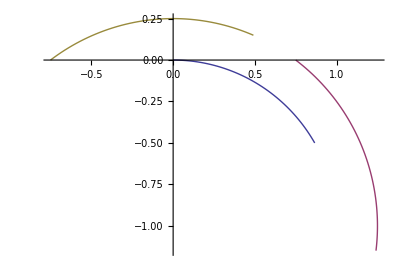

```mathematica
(* Use movement of right middle leg to get (rigid) movement of front/rear body segments. *)
gOC[t_] = oInit[SE2, Sin[t], Cos[t]-1, -t];
gRot[t_] = oInit[SE2, 0, 0, 0t];
gOCFlip[t_] = oInit[SE2, Sin[t], 1-Cos[t], t];
gCF = oInit[SE2, bodyLen/2, 0, 0];
gCB = oInit[SE2, -bodyLen/2, 0, 0];
ParametricPlot[{{gLocal[gOC[t]][[1]],gLocal[gOC[t]][[2]]},{gLocal[gOC[t].gCF][[1]], gLocal[gOC[t].gCF][[2]]},{gLocal[gOC[t].gCB][[1]], gLocal[gOC[t].gCB][[2]]}},{t,0,π/3}]

(* OBSERVATION: Cannot be as simple as a rotation of front/rear left-side legs. Need to work out the constrained parallel mechanism associated to tripod gait. Will be tricky. *)
```

### Math Associated to (Right) Tripod Gait Constraints